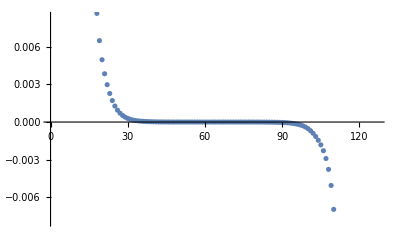

```mathematica
data = Import["/home/zortea/QuarkMesonModel/analysis/averaged.csv"];
ListPlot[data]
```

```mathematica
NonlinearModelFit[data, A Sinh[m*(128/2-x)], {A,m}, x, MaxIterations->1000]
```

FittedModel[2.91206×10^-7 Sinh[0.248224 (64-x)]]